# Deutsch-Jozsa Algorithm

Episode 29. Deutsch-Jozsa Algorithm

Episode 30. Bernstein-Vazirani Algorithm

Episode 31. Simon’s Algorithm

## Statement of the Problem

Consider a classical function f:{0, 1}^n→{0, 1}. It is a classical oracle taking n-bit inputs and returning 0 or 1.

The function is promised to be either constant (either 0 or 1 for all inputs) or balanced (0 for one half of the possible inputs and 1 for the other half).

The task is to determine whether f is constant or balanced by using the oracle the least number of times.

In classical algorithms, one has to evaluate the oracle (2^(n-1)+1)≈2^n/2 times in the worst case.

## Quantum Implementation

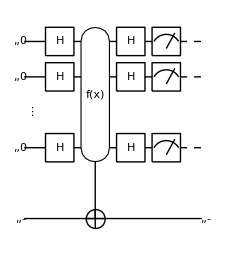

Figure 1. A quantum circuit for the Deutsch-Jozsa algorithm.

The first set of Hadamard gates:

0↦1/2^(n/2)Σ_(x=0)^(2^n-1)x

The quantum oracle:

1/2^(n/2)Σ_(x=0)^(2^n-1)x↦1/2^(n/2)Σ_(x=0)^(2^n-1)(x(-1))^(f(x))

The second set of Hadamard gates:

1/2^(n/2)Σ_(x=0)^(2^n-1)(x(-1))^(f(x))↦1/2^n Σ_(y=0)^(2^n-1)y(Σ_(x=0)^(2^n-1)(-1))^(f(x)+x·y)

To see the effect of the function f on the final state, suppose that f is a constant function. Then, the output state is given by

(-1)^(f(0))/2^n Σ_(y=0)^(2^n-1)(Σ_(x=0)^(2^n-1)(-1))^(x·y)=(-1)^(f(0))0.

Every measurement on each of the n qubits should yield zero with unit probability.

To make the analysis more explicit, consider the probability to find the n-qubit register in the state 0≡0⊗0⊗⋯⊗0

P_0=1/2^n(|(Σ_(x=0)^(2^n-1)(-1))^(f(x))|)^2.

If f is constant, then P_0=1.

When the function f is balanced, there are as many terms with −1 as 1, and the sum is always zero. There must be at least one qubit in the state 1 if the function f is balanced.

## Example

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Consider a balanced function as an example.

```mathematica
Clear[f];
f[{0,0}]=f[{1,0}]={0};
f[{0,1}]=f[{1,1}]={1};
```

Here is a quantum circuit for the Deutsch-Jozsa algorithm. The final Hadamard gate on the third qubit is not necessary, but we put it here to make the output state more readable.

```mathematica
cc={1,2};
tt={3};
all=Join[cc,tt];
qc=QuantumCircuit[Ket[S@tt->1,S@all],
S[all,6],Oracle[f,S@cc,S@tt],S[all,6],
"Invisible"->S@{2.5}]
```

```mathematica
out=ExpressionFor[qc]
```

## Summary

### Keywords

Oracle

Decision making

Detusch-Jozsa problem

### Functions

Oracle

### Related Links

Section 4.2 of the Quantum Workbook (2022, 2023).

Tutorial: Deutsch-Jozsa Algorithm